## Bounds on EDGB Theory From the Overall Posterior of GW151226

```mathematica
(*Originially I did seperate calculations of randomly selected 1000 dataset from the posterior and also for overall posterior. We found that it was better to consider the overall data since the results based on randomly selected data weren't consistent. I decided to keep the results only from overall dataset. Thats why many of the names I gave to differnt functions have the word 'all' with it. I just decided to keep it that way *)
```

```mathematica
dataOverall1=Import["/Users/stshammi/temp/EDGB_bound/GW151226/overall_post.csv","CSV"] ;(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import["/Users/stshammi/temp/EDGB_bound/GW151226/-1pn-all-beta.csv","CSV"] ; (*PPE beta*)
dataOverall3=Import["/Users/stshammi/temp/EDGB_bound/GW151226/-1pn-all-alpha.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
m1All=dataOverall1[[All,5]]*tsolar/.tsolar->4.925491*10^-6;
m2All=dataOverall1[[All,6]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1/1.64485*dataOverall2[[All,1]];(*1-sigma upper bound*)
αppEAll=1/1.64485*dataOverall3[[All,1]](*1-sigma upper bound*);
```

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] ;(*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

52252

```mathematica
Length[βppEAll]
```

52252

```mathematica
Mean[ζampAll]
```

12509.6

```mathematica
Mean[ζphaseAll]
```

360.999

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

51355

```mathematica
Length[ζAllampSelected]
```

46872

```mathematica
Mean[ζAllphaseSelected]
```

0.0174016

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.074786

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219},{0.789122,472.033,1.76752,0.97753,11.7264,10.59,0.967842,0.949848,0.436653,-0.301389,0.04629},52249,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},{0.789122,472.033,1.76752,0.97753,11.7264,10.59,0.967842,0.949848,0.436653,-0.301389,0.04629,1.58619},52249,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] (*Data satisfying zeta_phase<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},{0.789122,472.033,1.76752,0.97753,11.7264,10.59,0.967842,0.949848,0.436653,-0.301389},51351,{0.280777,395.397,3.53078,-0.343669,14.3417,8.84549,0.719679,0.111302,0.429138,0.208536},{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},{0.860122,617.575,3.77383,-0.740918,14.4537,8.68031,0.407971,0.658073,0.00252138,0.838901,0.00149139,0.0522075},46869,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A4[[All,12]]
```

{0.0171763,0.0522075,0.165549,0.0378357,0.0127864,0.0533918,0.0167203,0.0161527,0.129926,0.00981887,0.47965,0.00759042,46848,0.639428,0.00528177,0.0983506,0.0425141,0.0196601,0.0140803,0.0231292,0.000514475,0.0374042,0.727602,0.0315771,0.0686092}
 |  |  |  |

```mathematica
Length[A3]
```

51355

```mathematica
Length[A4]
```

46872

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.094265

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{4.81405,13.8985,6.13673,8.01727,12.5915,5.6388,4.50492,6.70477,4.82258,4.70667,7.63853,4.61487,10.3065,4.16243,52224,3.94756,11.1,3.81312,7.08526,5.78595,19.394,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

{2.015,5.74447,2.52291,3.29495,5.19042,2.31966,1.90965,2.94321,2.04561,1.98368,3.14457,2.10142,4.26331,1.84368,52225,4.61358,1.71006,2.90948,2.38032,7.96884,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

7.87527

```mathematica
Mean[SqrtαEDGBphase]
```

3.31329

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

{2.015,2.52291,3.29495,2.31966,1.90965,2.94321,2.04561,1.98368,3.14457,2.10142,4.26331,1.84368,1.80758,1.89248,46845,1.73059,4.61358,1.71006,2.90948,2.38032,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

{4.81405,6.13673,8.01727,5.6388,4.50492,6.70477,4.82258,4.70667,7.63853,4.61487,10.3065,4.16243,4.1191,4.01867,46844,6.49683,3.94756,11.1,3.81312,7.08526,5.78595,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

# Bounds from Phase Correction Using Compound Probability:

```mathematica
fun1=1/(√(2*π*(ζphaseAll)^2))*Exp[-x^2/(2Exp[2 Log[ζphaseAll]])] (*x is \[Zeta. and ζphaseAll is sigma_zeta from Fisher analysis*)
```

{756.691 ⅇ^(-1.79882×10^6 x^2),8.61832 ⅇ^(-233.343 x^2),267.496 ⅇ^(-224795. x^2),84.4682 ⅇ^(-22414.9 x^2),12.6478 ⅇ^(-502.549 x^2),52242,14667.2 ⅇ^(-6.75839×10^8 x^2),349.952 ⅇ^(-384739. x^2),19.0253 ⅇ^(-1137.14 x^2),437.105 ⅇ^(-600234. x^2),205.799 ⅇ^(-133056. x^2)}
 |  |  |  |

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

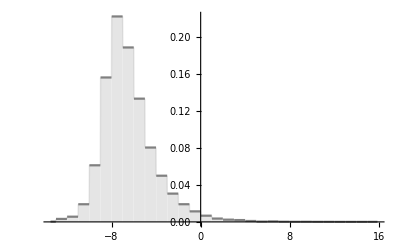

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

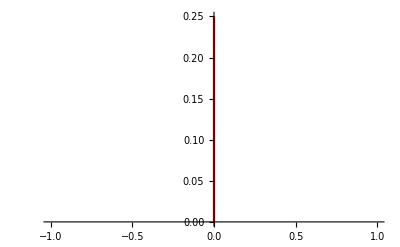

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red]
```

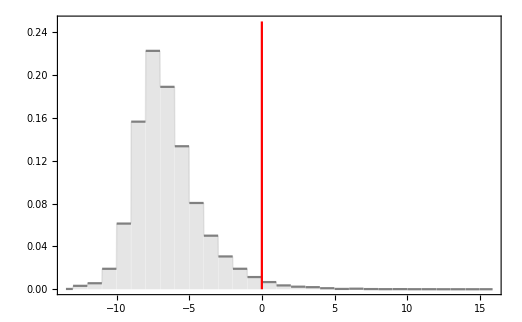

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] (*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Log[Max[ζphaseAll]]
```

15.8769

```mathematica
Log[Min[ζphaseAll]]
```

-13.4813

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.999836

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*98% area under the curve satisfies zeta<1 from phase correction*)
```

98.2835

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
Min[Log[ζampAll]]
```

-10.7176

```mathematica
Max[Log[ζampAll]]
```

19.4335

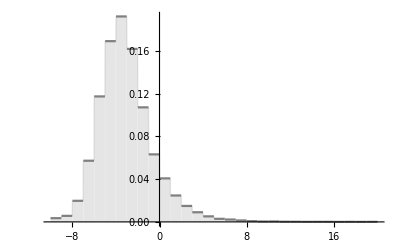

```mathematica
plottestamp=Plot[ps2amp[x],{x,-10,20},Filling->Axis,PlotStyle->Gray]
```

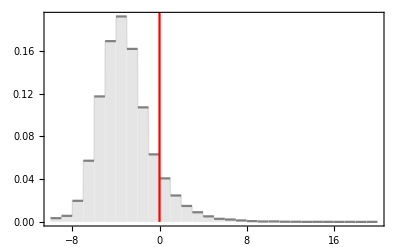

```mathematica
Show[plottestamp,zeta1,Frame->True]  (*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

89.7039

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.9998

```mathematica
fun2=PDF[𝒟log,Log[ζphaseAll]] (*pdf of log(sigma_zeta)|log_sigma_zeta*)
```

{0.222556,0.0500268,0.188969,0.133507,0.0500268,0.188969,0.222556,0.188969,0.222556,0.222556,0.133507,0.222556,52228,0.156453,0.133507,0.188969,0.019138,0.222556,0.222556,0.222556,0.0191189,0.188969,0.0500268,0.188969,0.188969}
 |  |  |  |

```mathematica
fun3=fun1*fun2
```

{168.406 ⅇ^(-1.79882×10^6 x^2),0.431147 ⅇ^(-233.343 x^2),50.5485 ⅇ^(-224795. x^2),11.2771 ⅇ^(-22414.9 x^2),0.632728 ⅇ^(-502.549 x^2),52242,280.42 ⅇ^(-6.75839×10^8 x^2),66.13 ⅇ^(-384739. x^2),0.951776 ⅇ^(-1137.14 x^2),82.5992 ⅇ^(-600234. x^2),38.8896 ⅇ^(-133056. x^2)}
 |  |  |  |

```mathematica
(*Length[fun3]*)
```

```mathematica
(*fun4=fun3/.x->0.0000001*)
```

```mathematica
fun5=Transpose[{Log[ζphaseAll],fun3}]
```

{{-7.54789,168.406 ⅇ^(-1.79882×10^6 x^2)},{-3.07283,0.431147 ⅇ^(-233.343 x^2)},{-6.50804,50.5485 ⅇ^(-224795. x^2)},52246,{-3.86471,0.951776 ⅇ^(-1137.14 x^2)},{-6.99911,82.5992 ⅇ^(-600234. x^2)},{-6.24584,38.8896 ⅇ^(-133056. x^2)}}
 |  |  |  |

```mathematica
(*fun6=Interpolation[fun5]*)(*Unless we give a specific value of x, NIntegrate is not possible*)
```

```mathematica
(*NIntegrate[fun6[z],{z,0,1}]*)
```

```mathematica
ΔζphaseAll=Table[Abs[Log[ζphaseAll[[i+1]]]-Log[ζphaseAll[[i]]]],{i,1,Length[βppEAll]-1}] (* delta sigma_zeta *)
```

{4.47507,3.43522,1.15273,1.89889,3.37108,0.964872,1.56901,1.29821,0.0602035,1.99088,2.17923,3.50452,3.87261,52225,4.27649,4.4922,2.57178,0.831329,4.90691,5.62326,0.0628702,0.236926,3.38505,3.73557,2.91202,3.1344,0.753273}
 |  |  |  |

```mathematica
fun7=Table[ΔζphaseAll[[i]]*fun3[[i]],{i,1,Length[ΔζphaseAll]}]
```

{753.629 ⅇ^(-1.79882×10^6 x^2),1.48108 ⅇ^(-233.343 x^2),58.2689 ⅇ^(-224795. x^2),21.414 ⅇ^(-22414.9 x^2),2.13298 ⅇ^(-502.549 x^2),52241,374.32 ⅇ^(-775580. x^2),1047.53 ⅇ^(-6.75839×10^8 x^2),192.572 ⅇ^(-384739. x^2),2.98325 ⅇ^(-1137.14 x^2),62.2197 ⅇ^(-600234. x^2)}
 |  |  |  |

```mathematica
fun8=Total[fun7] (*This is the pdf for zeta*)
```

1043.22 ⅇ^(-2.56248×10^11 x^2)+483.444 ⅇ^(-2.46016×10^11 x^2)+443.232 ⅇ^(-2.45214×10^11 x^2)+591.032 ⅇ^(-1.92737×10^11 x^2)+353.777 ⅇ^(-1.86371×10^11 x^2)+52242+1.43442×10^-10 ⅇ^(-5.84118×10^-13 x^2)+9.75673×10^-11 ⅇ^(-1.81222×10^-13 x^2)+4.83532×10^-11 ⅇ^(-8.85438×10^-15 x^2)+4.509×10^-11 ⅇ^(-8.09994×10^-15 x^2)
 |  |  |  |

```mathematica
(*fun8/.x->0.0000001*)
```

```mathematica
fun9[x_]=fun8
```

1043.22 ⅇ^(-2.56248×10^11 x^2)+483.444 ⅇ^(-2.46016×10^11 x^2)+443.232 ⅇ^(-2.45214×10^11 x^2)+591.032 ⅇ^(-1.92737×10^11 x^2)+353.777 ⅇ^(-1.86371×10^11 x^2)+52242+1.43442×10^-10 ⅇ^(-5.84118×10^-13 x^2)+9.75673×10^-11 ⅇ^(-1.81222×10^-13 x^2)+4.83532×10^-11 ⅇ^(-8.85438×10^-15 x^2)+4.509×10^-11 ⅇ^(-8.09994×10^-15 x^2)
 |  |  |  |

```mathematica
Sample= Table[10^-2*i,{i,-1000,1000}]//N;
```

```mathematica
points=Table[Sample[[i]],{i,1,2001}];(*These are the values of zeta that we are going to use for plotting the pdf of zeta. I am considering from -10 to 10 as suggested by you. But we don't know any good reason behind this except the fact that it is going to take more time if you go beyond this. Technincally, we are supposed to find the pdf upto 300, since it is mean of zeta from monte-carlo*)
```

```mathematica
pdfzeta=Map[fun9,points] (*This is going to take about five minutes.*)
```

General::munfl: Exp[-2.56248×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.46016×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45214×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
pdfzeta2=Transpose[{points,pdfzeta}];
```

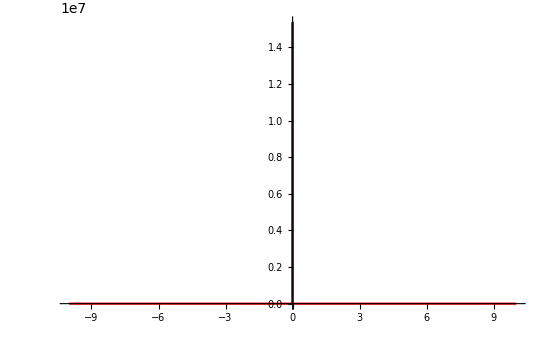

```mathematica
plot1=ListLinePlot[pdfzeta2,PlotStyle->Red,PlotRange->Full] (*You can use different plot range to see how it looks like*)
```

```mathematica
fun10=Interpolation[pdfzeta2,InterpolationOrder->1];
```

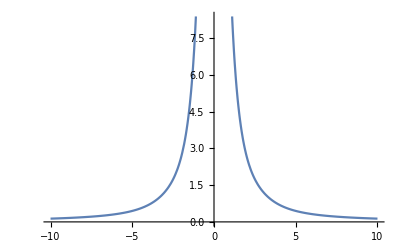

```mathematica
plot2=Plot[fun10[x],{x,-10,10},PlotRange->Automatic]
```

```mathematica
AreaPDF=(NIntegrate[fun10[z],{z,Min[points],Max[points]}]) (*To normalize the pdf*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.0387517}. NIntegrate obtained 77895.4 and 4866.66 for the integral and error estimates.

77895.4

```mathematica
pdfζphaseNormalized=Transpose[{points,pdfzeta/AreaPDF}];
```

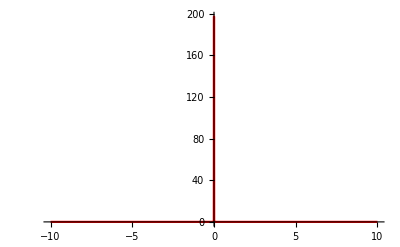

```mathematica
plot2=ListLinePlot[pdfζphaseNormalized,PlotStyle->Red,PlotRange->All] (*You can you use different plot range see how this function looks like*)
```

```mathematica
Meanζphase=Total[points*pdfzeta/AreaPDF] (*For a discrete pdf, this is how we derive expectation value- Σ Subscript[P, i] Subscript[ζ, i] , where Subscript[P, i] is the value of pdf at Subscript[ζ, i] . The expectation value is supposed to be zero, for some reason mathematica is giving a very small value*)
```

-3.03577×10^-18

```mathematica
stdevζphase=Sqrt[Total[(points-Meanζphase)^2*pdfzeta/AreaPDF]] (*This is the 1-sigma upper bound on zeta from the phase correction. The formula is Σ Subscript[P, i](Meanζ-Subscript[ζ, i])^2*)
```

0.539191

```mathematica
(*Now we are going to find bound on alpha_EDGB^2 from the selceted data that satisfies zeta<1. The reason of choosing this instead of square root of alpha_EDGB is that thisis proportional to ppE_beta. So we know that it's distribution is going to be Gaussian.*)
```

```mathematica
LogSqrtαPhase=Log[SqrtαEDGBphaseSelected^4] (*This is Log of sigma_(alpha^2)*)
```

{2.80248,3.70165,4.76956,3.36568,2.58768,4.31801,2.86279,2.73981,4.58271,2.97046,5.80019,2.44705,2.36796,2.55155,46845,2.19386,6.11602,2.14612,4.2719,3.46894,2.87685,3.45468,3.28,1.13134,3.44905,6.20047,3.21978,3.87642}
 |  |  |  |

```mathematica
𝒟logα=HistogramDistribution[LogSqrtαPhase]
```

DataDistribution[…]

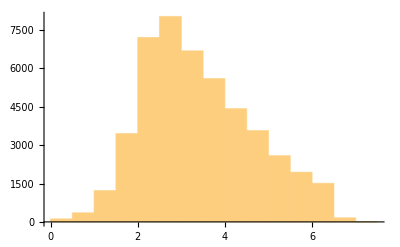

```mathematica
Histogram[LogSqrtαPhase]
```

```mathematica
func1=PDF[𝒟logα,LogSqrtαPhase] (*pdf of log(sigma_alphaEDGB^2)|log_sigma_alphaEDGB^2*)
```

{0.342635,0.239034,0.152244,0.285288,0.342635,0.188855,0.342635,0.342635,0.152244,0.342635,0.0829066,0.307561,0.307561,46846,0.307561,0.0643881,0.307561,0.188855,0.285288,0.342635,0.285288,0.285288,0.0522273,0.285288,0.0643881,0.285288,0.239034}
 |  |  |  |

```mathematica
func2=1/(√(2*π)*Exp[LogSqrtαPhase])*Exp[-x^2/(2Exp[2 LogSqrtαPhase])](*x is \[Zeta. and ζphaseAll is sigma_zeta from Fisher analysis of Overall dataset*)
```

{0.0241995 ⅇ^(-0.00183977 x^2),0.00984698 ⅇ^(-0.000304618 x^2),0.00338465 ⅇ^(-0.0000359897 x^2),0.0137788 ⅇ^(-0.000596451 x^2),0.0299981 ⅇ^(-0.00282707 x^2),46863,0.0126767 ⅇ^(-0.000504846 x^2),0.000809247 ⅇ^(-2.05737×10^-6 x^2),0.0159432 ⅇ^(-0.00079855 x^2),0.00826806 ⅇ^(-0.000214762 x^2)}
 |  |  |  |

```mathematica
func3=func1*func2
```

{0.0082916 ⅇ^(-0.00183977 x^2),0.00235376 ⅇ^(-0.000304618 x^2),0.000515295 ⅇ^(-0.0000359897 x^2),0.00393093 ⅇ^(-0.000596451 x^2),0.0102784 ⅇ^(-0.00282707 x^2),46863,0.00361649 ⅇ^(-0.000504846 x^2),0.0000521059 ⅇ^(-2.05737×10^-6 x^2),0.0045484 ⅇ^(-0.00079855 x^2),0.00197635 ⅇ^(-0.000214762 x^2)}
 |  |  |  |

```mathematica
ΔLogSqrtαPhase=Table[Abs[LogSqrtαPhase[[i+1]]-LogSqrtαPhase[[i]]],{i,1,Length[LogSqrtαPhase]-1}]
```

{0.899167,1.06791,1.40388,0.778,1.73033,1.45522,0.122976,1.8429,1.61225,2.82973,3.35314,0.0790819,0.183583,46845,1.73439,3.92216,3.96989,2.12578,0.802961,0.592087,0.577823,0.174674,2.14866,2.31771,2.75141,2.98068,0.656634}
 |  |  |  |

```mathematica
function5=Table[ΔLogSqrtαPhase[[i]]*func3[[i]],{i,1,Length[ΔLogSqrtαPhase]}]
```

{0.00745553 ⅇ^(-0.00183977 x^2),0.00251361 ⅇ^(-0.000304618 x^2),0.000723413 ⅇ^(-0.0000359897 x^2),0.00305826 ⅇ^(-0.000596451 x^2),0.017785 ⅇ^(-0.00282707 x^2),46862,0.0155787 ⅇ^(-0.0520352 x^2),0.00995046 ⅇ^(-0.000504846 x^2),0.000155311 ⅇ^(-2.05737×10^-6 x^2),0.00298664 ⅇ^(-0.00079855 x^2)}
 |  |  |  |

```mathematica
function5=Total[function5] (*This is the pdf of alpha_EDGB^2*)
```

0.00444267 ⅇ^(-0.483008 x^2)+0.00733614 ⅇ^(-0.473205 x^2)+0.00370568 ⅇ^(-0.426595 x^2)+0.00468619 ⅇ^(-0.425781 x^2)+0.00843587 ⅇ^(-0.425696 x^2)+46862+0.0000135372 ⅇ^(-4.98307×10^-7 x^2)+0.000010115 ⅇ^(-4.50047×10^-7 x^2)+0.0000121715 ⅇ^(-4.41789×10^-7 x^2)+9.65419×10^-9 ⅇ^(-4.00993×10^-7 x^2)
 |  |  |  |

```mathematica
function6[x_]=function5
```

0.00444267 ⅇ^(-0.483008 x^2)+0.00733614 ⅇ^(-0.473205 x^2)+0.00370568 ⅇ^(-0.426595 x^2)+0.00468619 ⅇ^(-0.425781 x^2)+0.00843587 ⅇ^(-0.425696 x^2)+46862+0.0000135372 ⅇ^(-4.98307×10^-7 x^2)+0.000010115 ⅇ^(-4.50047×10^-7 x^2)+0.0000121715 ⅇ^(-4.41789×10^-7 x^2)+9.65419×10^-9 ⅇ^(-4.00993×10^-7 x^2)
 |  |  |  |

```mathematica
Sample2= Table[10*i,{i,-100,100}]//N;
```

```mathematica
points2=Table[Sample2[[i]],{i,1,201}] ;(*These are the values of alpha_EDGB^2 that we are going to use for plotting the pdf*)
```

```mathematica
pdfα=Map[function6,points2] (*This is going to take about a minute*)
```

General::munfl: Exp[-483008.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-473205.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-426595.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0385934,0.040183,0.0418365,0.0435566,0.045346,0.0472077,0.0491447,0.0511601,0.0532574,0.05544,0.0577117,0.0600763,0.0625378,0.0651007,0.0677693,0.0705485,0.0734433,0.0764589,0.079601,0.0828755,0.0862886,0.089847,0.0935575,0.0974278,0.101466,0.105679,0.110078,0.114671,0.119469,0.124481,0.12972,0.135199,0.140929,0.146925,0.153202,0.159777,0.166666,0.173888,0.181463,0.189412,0.19776,0.206531,0.215751,0.225452,0.235664,0.246423,0.257767,0.269736,0.282377,0.295739,0.309876,0.32485,0.340725,0.357577,0.375486,0.394543,0.414849,0.436516,0.459672,0.484456,0.511029,0.539569,0.570277,0.603384,0.639147,0.677861,0.71986,0.765527,0.8153,0.869681,0.929251,0.994679,1.06675,1.14636,1.23458,1.33268,1.44214,1.56474,1.70262,1.85838,2.0352,2.23701,2.46878,2.73681,3.04925,3.41686,3.85402,4.38037,5.02322,5.82151,6.83231,8.14245,9.89015,12.3091,15.8278,21.318,30.7831,49.4426,92.6234,199.295,336.117,199.295,92.6234,49.4426,30.7831,21.318,15.8278,12.3091,9.89015,8.14245,6.83231,5.82151,5.02322,4.38037,3.85402,3.41686,3.04925,2.73681,2.46878,2.23701,2.0352,1.85838,1.70262,1.56474,1.44214,1.33268,1.23458,1.14636,1.06675,0.994679,0.929251,0.869681,0.8153,0.765527,0.71986,0.677861,0.639147,0.603384,0.570277,0.539569,0.511029,0.484456,0.459672,0.436516,0.414849,0.394543,0.375486,0.357577,0.340725,0.32485,0.309876,0.295739,0.282377,0.269736,0.257767,0.246423,0.235664,0.225452,0.215751,0.206531,0.19776,0.189412,0.181463,0.173888,0.166666,0.159777,0.153202,0.146925,0.140929,0.135199,0.12972,0.124481,0.119469,0.114671,0.110078,0.105679,0.101466,0.0974278,0.0935575,0.089847,0.0862886,0.0828755,0.079601,0.0764589,0.0734433,0.0705485,0.0677693,0.0651007,0.0625378,0.0600763,0.0577117,0.05544,0.0532574,0.0511601,0.0491447,0.0472077,0.045346,0.0435566,0.0418365,0.040183,0.0385934}

```mathematica
pdfα2=Transpose[{points2,pdfα}];
```

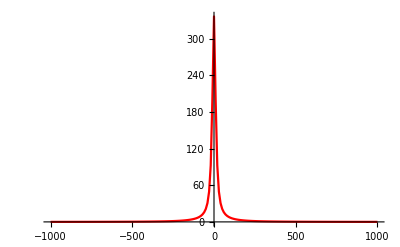

```mathematica
plot3=ListLinePlot[pdfα2,PlotStyle->Red,PlotRange->All]
```

```mathematica
function7=Interpolation[pdfα2,InterpolationOrder->1];
```

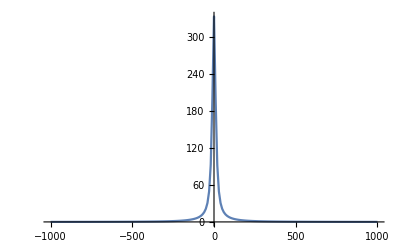

```mathematica
plot4=Plot[function7[x],{x,-1000,1000},PlotRange->All]
```

```mathematica
AreaPDFα=(NIntegrate[function7[z],{z,Min[points],Max[points]}]) (*To normalize the pdf*)
```

5354.11

```mathematica
pdfnormalizedα=Transpose[{points2,pdfα/AreaPDFα}];
```

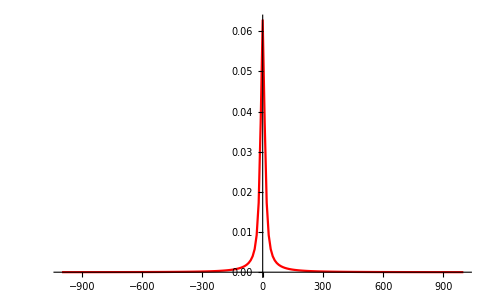

```mathematica
plot2=ListLinePlot[pdfnormalizedα,PlotStyle->Red,PlotRange->All]
```

```mathematica
Meanα=
Total[points2*pdfα/AreaPDFα] (*This is supposed to be zero*)
```

8.88178×10^-16

```mathematica
stdevα=Sqrt[Total[(points2-Meanα)^2*pdfα/AreaPDFα]] (*1-sigma upper bound on alpha_EDGB^2 *)
```

49.9274

```mathematica
√√stdevα (*Rough estimate of square root alpha_EDGB from phase correction*)
```

2.65818